```mathematica
R14=RotationMatrix[Subscript[θ, 14],{{0,0,0,1},{1,0,0,0}}];
R24=RotationMatrix[Subscript[θ, 24],{{0,0,0,1},{0,1,0,0}}];
R34=RotationMatrix[Subscript[θ, 34],{{0,0,0,1},{0,0,1,0}}];
R12=RotationMatrix[Subscript[θ, 12],{{0,1,0,0},{1,0,0,0}}];
R13=RotationMatrix[Subscript[θ, 13],{{0,0,1,0},{1,0,0,0}}];
R23=RotationMatrix[Subscript[θ, 23],{{0,0,1,0},{0,1,0,0}}];
```

```mathematica
(UPMNS=R23.R13.R12//Simplify)//MatrixForm
(U=R34.R24.R14.R23.R13.R12//Simplify)//MatrixForm
(U2010=R23.R24.R34.R14.R13.R12//Simplify)//MatrixForm
```

```mathematica
R23=RotationMatrix[Subscript[θ, 23],{{0,0,1,0},{0,1,0,0}}];
R23[[2,3]]=R23[[2,3]]*Exp[I delta23];R23[[3,2]]=R23[[3,2]]*Exp[I delta23];
R14=RotationMatrix[Subscript[θ, 14],{{0,0,0,1},{1,0,0,0}}];
R14[[1,4]]=R14[[1,4]]*Exp[I delta14];R14[[4,1]]=R14[[4,1]]*Exp[I delta14];
R13=RotationMatrix[Subscript[θ, 13],{{0,0,1,0},{1,0,0,0}}];
R13[[1,3]]=R13[[1,3]]*Exp[I delta13];R13[[3,1]]=R13[[3,1]]*Exp[I delta13];
R23//MatrixForm;
R14//MatrixForm;
R13//MatrixForm;
```

```mathematica
(U2010Complex=R23.R24.R34.R14.R13.R12//Simplify)//MatrixForm
```

(Cos[θ_12] Cos[θ_13] Cos[θ_14] | Cos[θ_13] Cos[θ_14] Sin[θ_12] | ⅇ^(ⅈ delta13) Cos[θ_14] Sin[θ_13] | ⅇ^(ⅈ delta14) Sin[θ_14]
-Cos[θ_23] Cos[θ_24] Sin[θ_12]+Cos[θ_12] (-ⅇ^(ⅈ delta14) Cos[θ_13] Sin[θ_14] (Cos[θ_23] Cos[θ_34] Sin[θ_24]+ⅇ^(ⅈ delta23) Sin[θ_23] Sin[θ_34])-ⅇ^(ⅈ delta13) Sin[θ_13] (ⅇ^(ⅈ delta23) Cos[θ_34] Sin[θ_23]-Cos[θ_23] Sin[θ_24] Sin[θ_34])) | Cos[θ_12] Cos[θ_23] Cos[θ_24]+Sin[θ_12] (-ⅇ^(ⅈ delta14) Cos[θ_13] Sin[θ_14] (Cos[θ_23] Cos[θ_34] Sin[θ_24]+ⅇ^(ⅈ delta23) Sin[θ_23] Sin[θ_34])-ⅇ^(ⅈ delta13) Sin[θ_13] (ⅇ^(ⅈ delta23) Cos[θ_34] Sin[θ_23]-Cos[θ_23] Sin[θ_24] Sin[θ_34])) | -ⅇ^(ⅈ (delta13+delta14)) Sin[θ_13] Sin[θ_14] (Cos[θ_23] Cos[θ_34] Sin[θ_24]+ⅇ^(ⅈ delta23) Sin[θ_23] Sin[θ_34])+Cos[θ_13] (ⅇ^(ⅈ delta23) Cos[θ_34] Sin[θ_23]-Cos[θ_23] Sin[θ_24] Sin[θ_34]) | Cos[θ_14] (Cos[θ_23] Cos[θ_34] Sin[θ_24]+ⅇ^(ⅈ delta23) Sin[θ_23] Sin[θ_34])
ⅇ^(ⅈ delta23) Cos[θ_24] Sin[θ_12] Sin[θ_23]+Cos[θ_12] (ⅇ^(ⅈ delta14) Cos[θ_13] Sin[θ_14] (ⅇ^(ⅈ delta23) Cos[θ_34] Sin[θ_23] Sin[θ_24]-Cos[θ_23] Sin[θ_34])-ⅇ^(ⅈ delta13) Sin[θ_13] (Cos[θ_23] Cos[θ_34]+ⅇ^(ⅈ delta23) Sin[θ_23] Sin[θ_24] Sin[θ_34])) | -ⅇ^(ⅈ delta23) Cos[θ_12] Cos[θ_24] Sin[θ_23]+Sin[θ_12] (ⅇ^(ⅈ delta14) Cos[θ_13] Sin[θ_14] (ⅇ^(ⅈ delta23) Cos[θ_34] Sin[θ_23] Sin[θ_24]-Cos[θ_23] Sin[θ_34])-ⅇ^(ⅈ delta13) Sin[θ_13] (Cos[θ_23] Cos[θ_34]+ⅇ^(ⅈ delta23) Sin[θ_23] Sin[θ_24] Sin[θ_34])) | ⅇ^(ⅈ (delta13+delta14)) Sin[θ_13] Sin[θ_14] (ⅇ^(ⅈ delta23) Cos[θ_34] Sin[θ_23] Sin[θ_24]-Cos[θ_23] Sin[θ_34])+Cos[θ_13] (Cos[θ_23] Cos[θ_34]+ⅇ^(ⅈ delta23) Sin[θ_23] Sin[θ_24] Sin[θ_34]) | Cos[θ_14] (-ⅇ^(ⅈ delta23) Cos[θ_34] Sin[θ_23] Sin[θ_24]+Cos[θ_23] Sin[θ_34])
Sin[θ_12] Sin[θ_24]-Cos[θ_12] Cos[θ_24] (ⅇ^(ⅈ delta14) Cos[θ_13] Cos[θ_34] Sin[θ_14]-ⅇ^(ⅈ delta13) Sin[θ_13] Sin[θ_34]) | -Cos[θ_12] Sin[θ_24]-Cos[θ_24] Sin[θ_12] (ⅇ^(ⅈ delta14) Cos[θ_13] Cos[θ_34] Sin[θ_14]-ⅇ^(ⅈ delta13) Sin[θ_13] Sin[θ_34]) | -Cos[θ_24] (ⅇ^(ⅈ (delta13+delta14)) Cos[θ_34] Sin[θ_13] Sin[θ_14]+Cos[θ_13] Sin[θ_34]) | Cos[θ_14] Cos[θ_24] Cos[θ_34])

```mathematica
multiTaylor[f_,{vars_?VectorQ,pt_?VectorQ,n_Integer?NonNegative}]:=Sum[Nest[(vars-pt).#&,(D[f,{vars,k}]/.Thread[vars->pt]),k]/k!,{k,0,n},Method->"Procedural"]
```

```mathematica
multiTaylor[multiTaylor[multiTaylor[Series[U[[1,1]]^2,{Subscript[θ, 24],0,2},{Subscript[θ, 14],0,2},{Subscript[θ, 34],0,2},{Subscript[θ, 34],0,2}]//FullSimplify//Normal,{{Subscript[θ, 14] ,Subscript[θ, 24]},{0,0},2}],{{Subscript[θ, 14] ,Subscript[θ, 34]},{0,0},2}],{{Subscript[θ, 24] ,Subscript[θ, 34]},{0,0},2}]//Simplify
multiTaylor[multiTaylor[multiTaylor[Series[U[[1,2]]^2,{Subscript[θ, 24],0,2},{Subscript[θ, 14],0,2},{Subscript[θ, 34],0,2},{Subscript[θ, 34],0,2}]//FullSimplify//Normal,{{Subscript[θ, 14] ,Subscript[θ, 24]},{0,0},2}],{{Subscript[θ, 14] ,Subscript[θ, 34]},{0,0},2}],{{Subscript[θ, 24] ,Subscript[θ, 34]},{0,0},2}]//Simplify
multiTaylor[multiTaylor[multiTaylor[Series[U[[1,3]]^2,{Subscript[θ, 24],0,2},{Subscript[θ, 14],0,2},{Subscript[θ, 34],0,2},{Subscript[θ, 34],0,2}]//FullSimplify//Normal,{{Subscript[θ, 14] ,Subscript[θ, 24]},{0,0},2}],{{Subscript[θ, 14] ,Subscript[θ, 34]},{0,0},2}],{{Subscript[θ, 24] ,Subscript[θ, 34]},{0,0},2}]//Simplify
```

-Cos[θ_12]^2 Cos[θ_13]^2 (-1+θ_14^2)

-Cos[θ_13]^2 Sin[θ_12]^2 (-1+θ_14^2)

-Sin[θ_13]^2 (-1+θ_14^2)

## 2010 parametrization

```mathematica
ExpandSterile[U_,order_]:=multiTaylor[multiTaylor[multiTaylor[Series[U,{Subscript[θ, 24],0,order},{Subscript[θ, 14],0,order},{Subscript[θ, 34],0,order}]//FullSimplify//Normal,{{Subscript[θ, 14] ,Subscript[θ, 24]},{0,0},order}],{{Subscript[θ, 14] ,Subscript[θ, 34]},{0,0},order}],{{Subscript[θ, 24] ,Subscript[θ, 34]},{0,0},order}]//Simplify
```

### Full matrix

```mathematica
U2010LO = U2010;
U2010LOComplex = U2010Complex;
```

```mathematica
For[i=1,i<5,i++,For[j=1,j<5,j++,U2010LO[[i,j]] = ExpandSterile[U2010[[i,j]]/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]},1]]]
For[i=1,i<5,i++,For[j=1,j<5,j++,U2010LOComplex[[i,j]] = ExpandSterile[U2010Complex[[i,j]]/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]},1]]]
```

```mathematica
U2010LO//MatrixForm
U2010LOComplex//MatrixForm
```

(Cos[θ_12] Cos[θ_13] | Cos[θ_13] Sin[θ_12] | Sin[θ_13] | θ_14
-Cos[θ_23] Sin[θ_12]-Cos[θ_12] Sin[θ_13] Sin[θ_23] | Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23] | Cos[θ_13] Sin[θ_23] | Sec[θ_23] θ_24
-Cos[θ_12] Cos[θ_23] Sin[θ_13]+Sin[θ_12] Sin[θ_23] | -Cos[θ_23] Sin[θ_12] Sin[θ_13]-Cos[θ_12] Sin[θ_23] | Cos[θ_13] Cos[θ_23] | 0
-Cos[θ_12] Cos[θ_13] θ_14+θ_24 (Sin[θ_12]+Cos[θ_12] Sin[θ_13] Tan[θ_23]) | -Cos[θ_13] Sin[θ_12] θ_14+θ_24 (-Cos[θ_12]+Sin[θ_12] Sin[θ_13] Tan[θ_23]) | -Sin[θ_13] θ_14-Cos[θ_13] θ_24 Tan[θ_23] | 1)

(Cos[θ_12] Cos[θ_13] | Cos[θ_13] Sin[θ_12] | ⅇ^(ⅈ delta13) Sin[θ_13] | ⅇ^(ⅈ delta14) θ_14
-Cos[θ_23] Sin[θ_12]-ⅇ^(ⅈ (delta13+delta23)) Cos[θ_12] Sin[θ_13] Sin[θ_23] | Cos[θ_12] Cos[θ_23]-ⅇ^(ⅈ (delta13+delta23)) Sin[θ_12] Sin[θ_13] Sin[θ_23] | ⅇ^(ⅈ delta23) Cos[θ_13] Sin[θ_23] | θ_24 (Cos[θ_23]+ⅇ^(ⅈ delta23) Sin[θ_23] Tan[θ_23])
-ⅇ^(ⅈ delta13) Cos[θ_12] Cos[θ_23] Sin[θ_13]+ⅇ^(ⅈ delta23) Sin[θ_12] Sin[θ_23] | -ⅇ^(ⅈ delta13) Cos[θ_23] Sin[θ_12] Sin[θ_13]-ⅇ^(ⅈ delta23) Cos[θ_12] Sin[θ_23] | Cos[θ_13] Cos[θ_23] | -(-1+ⅇ^(ⅈ delta23)) Sin[θ_23] θ_24
-ⅇ^(ⅈ delta14) Cos[θ_12] Cos[θ_13] θ_14+θ_24 (Sin[θ_12]+ⅇ^(ⅈ delta13) Cos[θ_12] Sin[θ_13] Tan[θ_23]) | -ⅇ^(ⅈ delta14) Cos[θ_13] Sin[θ_12] θ_14+θ_24 (-Cos[θ_12]+ⅇ^(ⅈ delta13) Sin[θ_12] Sin[θ_13] Tan[θ_23]) | -ⅇ^(ⅈ (delta13+delta14)) Sin[θ_13] θ_14-Cos[θ_13] θ_24 Tan[θ_23] | 1)

### Nunew basis

```mathematica
A=R23.R24.R34.R13.R13;
ALO=A;
For[i=1,i<5,i++,For[j=1,j<5,j++,ALO[[i,j]] = ExpandSterile[A[[i,j]]/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]},1]]]
ALO//MatrixForm
```

(Cos[2 θ_13] | 0 | Sin[2 θ_13] | 0
-Sin[2 θ_13] Sin[θ_23] | Cos[θ_23] | Cos[2 θ_13] Sin[θ_23] | Sec[θ_23] θ_24
-Cos[θ_23] Sin[2 θ_13] | -Sin[θ_23] | Cos[2 θ_13] Cos[θ_23] | 0
Sin[2 θ_13] θ_24 Tan[θ_23] | -θ_24 | -Cos[2 θ_13] θ_24 Tan[θ_23] | 1)

```mathematica
Transpose[ALO].{{nue},{numu},{nutau},{nus}}//Simplify//MatrixForm
R12.{{nu1},{nu2},{nu3},{nu4}}//MatrixForm
```

(nue Cos[2 θ_13]-Sin[2 θ_13] (nutau Cos[θ_23]+numu Sin[θ_23])+nus Sin[2 θ_13] θ_24 Tan[θ_23]
numu Cos[θ_23]-nutau Sin[θ_23]-nus θ_24
nue Sin[2 θ_13]+Cos[2 θ_13] (nutau Cos[θ_23]+numu Sin[θ_23])-nus Cos[2 θ_13] θ_24 Tan[θ_23]
nus+numu Sec[θ_23] θ_24)

(nu1 Cos[θ_12]+nu2 Sin[θ_12]
nu2 Cos[θ_12]-nu1 Sin[θ_12]
nu3
nu4)

```mathematica
ALO.{{nu1},{nu2},{nu3},{nu4}}//MatrixForm
```

(nu1 Cos[2 θ_13]+nu3 Sin[2 θ_13]
nu2 Cos[θ_23]+nu3 Cos[2 θ_13] Sin[θ_23]-nu1 Sin[2 θ_13] Sin[θ_23]+nu4 Sec[θ_23] θ_24
nu3 Cos[2 θ_13] Cos[θ_23]-nu1 Cos[θ_23] Sin[2 θ_13]-nu2 Sin[θ_23]
nu4-nu2 θ_24-nu3 Cos[2 θ_13] θ_24 Tan[θ_23]+nu1 Sin[2 θ_13] θ_24 Tan[θ_23])

```mathematica
Transpose[ALO].ALO//Simplify
```

{{1+Sin[2 θ_13]^2 θ_24^2 Tan[θ_23]^2,-Sin[2 θ_13] θ_24^2 Tan[θ_23],-1/2 Sin[4 θ_13] θ_24^2 Tan[θ_23]^2,0},{-Sin[2 θ_13] θ_24^2 Tan[θ_23],1+θ_24^2,Cos[2 θ_13] θ_24^2 Tan[θ_23],0},{-1/2 Sin[4 θ_13] θ_24^2 Tan[θ_23]^2,Cos[2 θ_13] θ_24^2 Tan[θ_23],1+Cos[2 θ_13]^2 θ_24^2 Tan[θ_23]^2,0},{0,0,0,1+Sec[θ_23]^2 θ_24^2}}

```mathematica
a=U2010LO[[4,1]]^2/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]}/.{Subscript[θ, 14]-> Ue4,Subscript[θ, 24]-> Umu4/Sec[Subscript[θ, 23]]}//FullSimplify
b=U2010LO[[4,2]]^2/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]}/.{Subscript[θ, 14]-> Ue4,Subscript[θ, 24]-> Umu4/Sec[Subscript[θ, 23]]}//FullSimplify
c=U2010LO[[4,3]]^2/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]}/.{Subscript[θ, 14]-> Ue4,Subscript[θ, 24]-> Umu4/Sec[Subscript[θ, 23]]}//FullSimplify
```

(Umu4 Cos[θ_23] Sin[θ_12]+Cos[θ_12] (-Ue4 Cos[θ_13]+Umu4 Sin[θ_13] Sin[θ_23]))^2

(Umu4 Cos[θ_12] Cos[θ_23]+Sin[θ_12] (Ue4 Cos[θ_13]-Umu4 Sin[θ_13] Sin[θ_23]))^2

(Ue4 Sin[θ_13]+Umu4 Cos[θ_13] Sin[θ_23])^2

```mathematica
acomplex=(U2010LOComplex[[4,1]]*(U2010LOComplex[[4,1]]/.{delta13-> -delta13,delta23-> -delta23,delta14-> -delta14}))/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]}/.{Subscript[θ, 14]-> Ue4,Subscript[θ, 24]-> Umu4/Sec[Subscript[θ, 23]]}//FullSimplify
bcomplex=(U2010LOComplex[[4,2]]*(U2010LOComplex[[4,2]]/.{delta13-> -delta13,delta23-> -delta23,delta14-> -delta14}))/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]}/.{Subscript[θ, 14]-> Ue4,Subscript[θ, 24]-> Umu4/Sec[Subscript[θ, 23]]}//FullSimplify
ccomplex=(U2010LOComplex[[4,3]]*(U2010LOComplex[[4,3]]/.{delta13-> -delta13,delta23-> -delta23,delta14-> -delta14}))/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]}/.{Subscript[θ, 14]-> Ue4,Subscript[θ, 24]-> Umu4/Sec[Subscript[θ, 23]]}//FullSimplify
```

(Umu4 Cos[θ_23] Sin[θ_12]+Cos[θ_12] (-ⅇ^(-ⅈ delta14) Ue4 Cos[θ_13]+ⅇ^(-ⅈ delta13) Umu4 Sin[θ_13] Sin[θ_23])) (Umu4 Cos[θ_23] Sin[θ_12]+Cos[θ_12] (-ⅇ^(ⅈ delta14) Ue4 Cos[θ_13]+ⅇ^(ⅈ delta13) Umu4 Sin[θ_13] Sin[θ_23]))

(-Umu4 Cos[θ_12] Cos[θ_23]+Sin[θ_12] (-ⅇ^(-ⅈ delta14) Ue4 Cos[θ_13]+ⅇ^(-ⅈ delta13) Umu4 Sin[θ_13] Sin[θ_23])) (-Umu4 Cos[θ_12] Cos[θ_23]-Sin[θ_12] (ⅇ^(ⅈ delta14) Ue4 Cos[θ_13]-ⅇ^(ⅈ delta13) Umu4 Sin[θ_13] Sin[θ_23]))

Ue4^2 Sin[θ_13]^2+Umu4 Sin[θ_23] (Ue4 Cos[delta13+delta14] Sin[2 θ_13]+Umu4 Cos[θ_13]^2 Sin[θ_23])

```mathematica
b*c/.{Ue4-> 0}//FullSimplify
bcomplex*ccomplex//FullSimplify
```

Umu4^4 Cos[θ_13]^2 Sin[θ_23]^2 (Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23])^2

$Aborted

Umu4^4 (Cos[θ_23] Sin[θ_12]+Cos[θ_12] Sin[θ_13] Sin[θ_23])^2 (Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23])^2

$Aborted

```mathematica
a*b/.{Ue4-> 0}//FullSimplify
a*b-acomplex*bcomplex//ComplexExpand//Simplify
```

```mathematica
a/.{Subscript[θ, 12]->π/2,Subscript[θ, 13]-> 0}
b/.{Subscript[θ, 12]->π/2,Subscript[θ, 13]-> 0}
c/.{Subscript[θ, 12]->π/2,Subscript[θ, 13]-> 0}
```

Umu4^2 Cos[θ_23]^2

Ue4^2

Umu4^2 Sin[θ_23]^2

```mathematica
ae=U2010LO[[1,1]]^2/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]}/.{Subscript[θ, 12]-> T12}//FullSimplify
be=U2010LO[[1,2]]^2/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]}/.{Subscript[θ, 12]-> T12}//FullSimplify
ce=U2010LO[[1,3]]^2/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]}/.{Subscript[θ, 12]-> T12}//FullSimplify
am=U2010LO[[2,1]]^2/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]}/.{Subscript[θ, 12]-> T12}//FullSimplify
bm=U2010LO[[2,2]]^2/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]}/.{Subscript[θ, 12]-> T12}//FullSimplify
cm=U2010LO[[2,3]]^2/.{Subscript[θ, 34]-> Tan[Subscript[θ, 23]] Subscript[θ, 24]}/.{Subscript[θ, 12]-> T12}//FullSimplify
```

Cos[T12]^2 Cos[θ_13]^2

Cos[θ_13]^2 Sin[T12]^2

Sin[θ_13]^2

(Cos[θ_23] Sin[T12]+Cos[T12] Sin[θ_13] Sin[θ_23])^2

(Cos[T12] Cos[θ_23]-Sin[T12] Sin[θ_13] Sin[θ_23])^2

Cos[θ_13]^2 Sin[θ_23]^2

```mathematica
Pse = ae * a+be*b+ce*c//Simplify
```

Sin[θ_13]^2 (Ue4 Sin[θ_13]+Umu4 Cos[θ_13] Sin[θ_23])^2+Cos[θ_13]^2 Sin[T12]^2 (Umu4 Cos[θ_12] Cos[θ_23]+Sin[θ_12] (Ue4 Cos[θ_13]-Umu4 Sin[θ_13] Sin[θ_23]))^2+Cos[T12]^2 Cos[θ_13]^2 (Umu4 Cos[θ_23] Sin[θ_12]+Cos[θ_12] (-Ue4 Cos[θ_13]+Umu4 Sin[θ_13] Sin[θ_23]))^2

```mathematica
Pse/.{Ue4-> 0}//FullSimplify
Pse/.{Umu4-> 0}//FullSimplify
```

Cos[θ_13]^2 (Umu4^2 Sin[θ_13]^2 Sin[θ_23]^2+Cos[T12]^2 (Umu4 Cos[θ_23] Sin[θ_12]+Umu4 Cos[θ_12] Sin[θ_13] Sin[θ_23])^2+Sin[T12]^2 (Umu4 Cos[θ_12] Cos[θ_23]-Umu4 Sin[θ_12] Sin[θ_13] Sin[θ_23])^2)

Ue4^2 (1/2 (1+Cos[2 T12] Cos[2 θ_12]) Cos[θ_13]^4+Sin[θ_13]^4)

```mathematica
D[D[Pse,{Umu4}],{Ue4}]/.{Subscript[θ, 13]-> 0}//FullSimplify
```

-Cos[2 T12] Cos[θ_23] Sin[2 θ_12]

```mathematica
Pse/.{Ue4-> 0,Subscript[θ, 13]-> 0}//FullSimplify
```

-1/2 Umu4^2 (-1+Cos[2 T12] Cos[2 θ_12]) Cos[θ_23]^2

```mathematica
ae/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324, Umu4-> r Ue4}//Simplify
be/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324, Umu4-> r Ue4}//Simplify
ce/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324, Umu4-> r Ue4}//Simplify
```

0.680866

0.29739

0.0217445

```mathematica
r=0.1;
```

```mathematica
a/(Umu4^2+Ue4^2)/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324, Umu4-> r Ue4}//Simplify
b/(Umu4^2+Ue4^2)/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324, Umu4-> r Ue4}//Simplify
c/(Umu4^2+Ue4^2)/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324, Umu4-> r Ue4}//Simplify
```

0.596305

0.358371

0.045324

```mathematica
(Umu4^2 am+Ue4^2ae)/(Umu4^2+Ue4^2)/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324, Umu4-> r Ue4}//Simplify
 (Umu4^2 bm+Ue4^2be)/(Umu4^2+Ue4^2)/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324, Umu4-> r Ue4}//Simplify
(Umu4^2 cm+Ue4^2ce)/(Umu4^2+Ue4^2)/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324, Umu4-> r Ue4}//Simplify
```

0.67651

0.297583

0.0259072

```mathematica
a*c/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324,Ue4-> 0.1,Umu4-> √(10^-4)}//FullSimplify
```

2.75702×10^-6

```mathematica
dmSQR21 = 7.5*10^-5(*eV^2*)
```

0.000075

```mathematica
Ve =
```

```mathematica
Epsilon12[E_]:=(2Ve E)/dmSQR21
```

```mathematica
DeltaM21[E_]:=dmSQR21/(2E)√((Cos[2 Subscript[θ, 12]]-Cos[Subscript[θ, 13]]^2 Epsilon12[E])^2+(Sin[2 Subscript[θ, 12]])^2)
```

```mathematica
Freg[E_,L_]:=(Cos[Subscript[θ, 13]])^4*(Sin[2*Subscript[θ, 12]])^2*Ve/DeltaM21[E]*(Sin[1/2 DeltaM21[E]*L])^2
```

```mathematica
P1ef[E_]:= (Cos[Subscript[θ, 13]]^2*Cos[Subscript[θ, 12]]^2-Freg[E*10^6,637*10^6*(1.973*10^-5)^-1])/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324,Ve->-2*10^-13}
P2ef[E_]:=1-Sin[ 0.148]^2-P1ef[E]
```

```mathematica
P1e=Cos[Subscript[θ, 13]]^2*Cos[Subscript[θ, 12]]^2/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324,Ve-> 2*2*10^-13}
P2e=Cos[Subscript[θ, 13]]^2*Sin[Subscript[θ, 12]]^2/.{Subscript[θ, 13]-> 0.148,Subscript[θ, 12]->0.583996,T12->0.583996,Subscript[θ, 23]->0.737324,Ve->2* 2*10^-13}
```

0.680866

0.29739

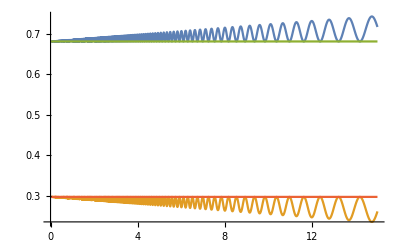

```mathematica
Plot[{P1ef[x],P2ef[x],P1e,P2e},{x,0,15}]
```